```mathematica
fub ={1,1,2,3,5,8,13,21,34}
```

{1,1,2,3,5,8,13,21,34}

```mathematica
fubi=Table[Fibonacci[n],{n,10}];
```

```mathematica
funktionexp=a Exp[(-b (x))];
```

```mathematica
ff=FindFit[fubi,funktionexp,{a,b},x]
```

{a→0.448078,b→-0.481006}

```mathematica
fubb=Function[{x},Evaluate[funktionexp/. ff]]
```

Function[{x},0.448643 ⅇ^(0.480844 x)]

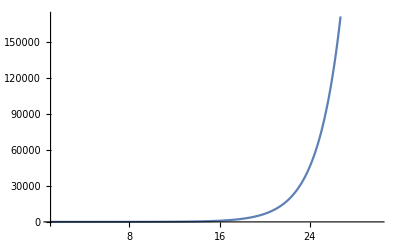

```mathematica
Plot[fubb[x],{x,1,30}]
```

```mathematica
Quit[]
```

```mathematica
gg=DSolve[{x'[t]==r x[t](k-x[t])/k, x[0]==x0}, x[t], t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x[t]→(ⅇ^(r t) k x0)/(k-x0+ⅇ^(r t) x0)}}

```mathematica
Clear[k]
```

```mathematica
{{x[t]->(ⅇ^(r t) k x0)/(k-x0+ⅇ^(r t) x0)}}
```

```mathematica
{{x[t]->(0.44864290381890265 ⅇ^(0.480844 t) k)/(-0.44864290381890265+0.44864290381890265 ⅇ^(0.480844 t)+k)}}
```

```mathematica
cj=(448.64290381890265 ⅇ^(0.480844 t))/(999.551357096181+0.44864290381890265 ⅇ^(0.480844 t))
```

(448.643 ⅇ^(0.480844 t))/(999.551+0.448643 ⅇ^(0.480844 t))

```mathematica
x0= 0.44864290381890265 ;
```

```mathematica
r=0.480844;
```

```mathematica
Plot[(448.64290381890265 ⅇ^(0.480844 t))/(999.551357096181+0.44864290381890265 ⅇ^(0.480844 t)),{t,0,30}]
```

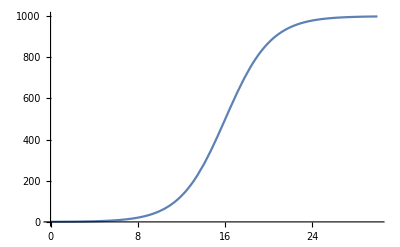

-Graphics-

```mathematica
Manipulate[Plot[(0.44864290381890265 ⅇ^(0.480844 t) k)/(-0.44864290381890265+0.44864290381890265 ⅇ^(0.480844 t)+k),{t,0,30}],{k,1,1000}]
```